```mathematica
Quit
```

# Formatting of axes - part 2

```mathematica
f[x_]:= x^2;
```

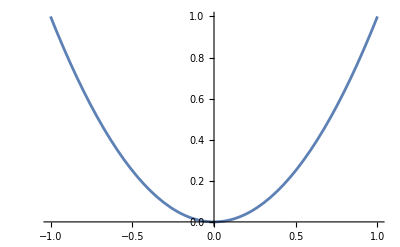

```mathematica
Plot[f[x],{x,-1,1}]
```

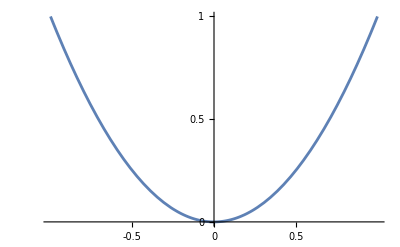

```mathematica
Plot[f[x],{x,-1,1},Ticks->{{-0.5,0,0.5},{0,0.5,1}},TicksStyle->Directive[Orange,12]]
```

```mathematica
Plot[f[x],{x,-1,1},Ticks->{{-0.5,0,0.5},{0,0.5,1}},TicksStyle->{Red,Blue}]
```

-Graphics-

```mathematica
Plot[f[x],{x,-1,1},AxesStyle->Directive[Blue,Dashed]]
```

-Graphics-

```mathematica
Plot[f[x],{x,-1,1},AxesStyle->Directive[Red,Dashed]]
```

-Graphics-

```mathematica
Plot[f[x],{x,-1,1},AxesStyle->Directive[Gray,Dashed]]
```

-Graphics-

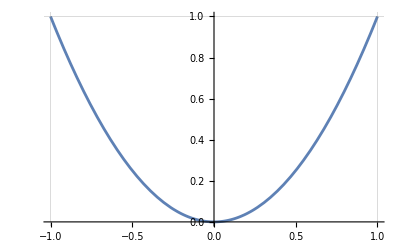

```mathematica
Plot[f[x],{x,-1,1},GridLines->{{-1,1},{1}}]
```

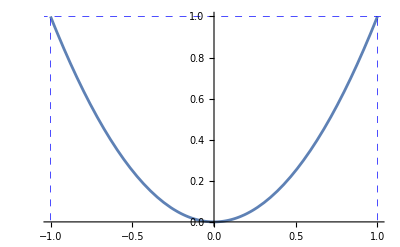

```mathematica
Plot[f[x],{x,-1,1},GridLines->{{-1,1},{1}},GridLinesStyle->Directive[Blue,Dashed]]
```

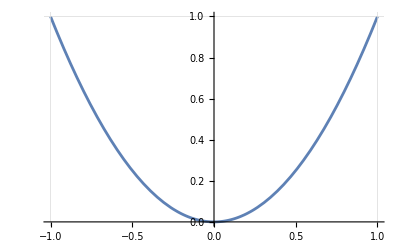

```mathematica
Plot[f[x],{x,-1,1},GridLines->{{-1,1},{1}},GridLinesStyle->{{Blue,Dashed},{Gray,Dotted}}]
```